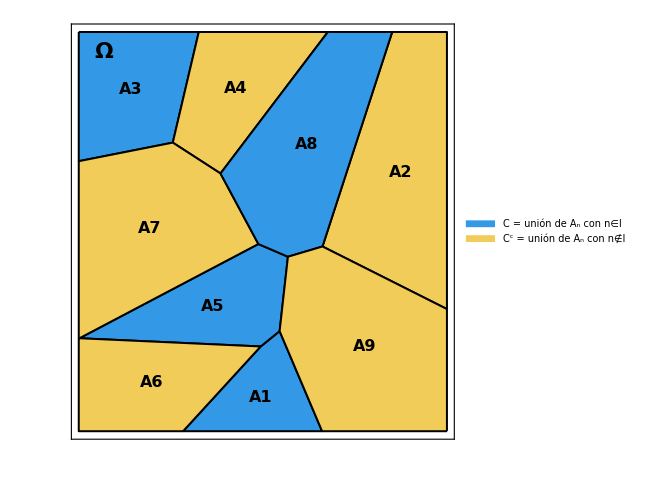

```mathematica
SeedRandom[3];
nBloques=9;
puntosSemilla=RandomReal[{0.5,5.5},{nBloques,2}];

vmesh=VoronoiMesh[puntosSemilla,{{0,6},{0,6}}];
celdas=MeshPrimitives[vmesh,2];

indicesI={1,3,5,8}; (*subconjunto de índices I que define C*)

colorC=RGBColor[0.2,0.6,0.9];
colorCc=RGBColor[0.95,0.8,0.35];

coloresCelda=Table[If[MemberQ[indicesI,n],colorC,colorCc],{n,nBloques}];

celdasColoreadas=Table[{coloresCelda[[n]],EdgeForm[{Black,Thickness[0.003]}],celdas[[n]]},{n,nBloques}];

etiquetas=Table[Text[Style["A"<>ToString[n],16,Bold,Black],RegionCentroid[celdas[[n]]]],{n,nBloques}];

grafico=Graphics[{celdasColoreadas,etiquetas,Text[Style["Ω",22,Bold],{0.4,5.7}]},PlotRange->{{0,6},{0,6}},ImageSize->480,Frame->True,FrameStyle->Black,FrameTicks->None];

Legended[grafico,SwatchLegend[{colorC,colorCc},{"C = unión de Aₙ con n∈I","Cᶜ = unión de Aₙ con n∉I"},LabelStyle->Directive[FontSize->16],LegendMarkerSize->20]]
```

```mathematica
Export["C:\\Users\\jesus\\Desktop\\Universidad\\Teoría de la probabilidad\\Latex_Teoria_Probabilidad\\imagenes\\problemas_Quesada\\prob_quesada_1_22_a.png",%73,"PNG"]
```

C:\Users\jesus\Desktop\Universidad\Teoría de la probabilidad\Latex_Teoria_Probabilidad\imagenes\problemas_Quesada\prob_quesada_1_22_a.png